-Graphics3D-

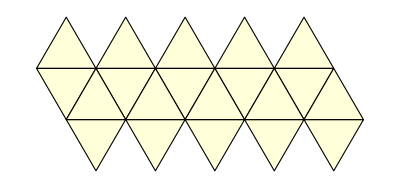

{{1,3},{1,5},{1,6},{1,9},{1,10},{2,4},{2,7},{2,8},{2,11},{2,12},{3,7},{3,8},{3,9},{3,10},{4,5},{4,6},{4,11},{4,12},{5,6},{5,9},{5,11},{6,10},{6,12},{7,8},{7,9},{7,11},{8,10},{8,12},{9,11},{10,12}}

-Graphics3D-

```mathematica
(* use icosahedron function*)
Graphics3D[Icosahedron[], Boxed->False]
PolyhedronData["Icosahedron", "Net"]
vertices=PolyhedronData["Icosahedron","VertexCoordinates"];
edges = PolyhedronData["Icosahedron", "EdgeIndices"]
faces = PolyhedronData["Icosahedron", "FaceIndices"];Graphics3D[{PolyhedronData["Icosahedron","Faces"],Table[Text[Style[i,Bold,16],vertices[[i]]],{i,Length[vertices]}]},Boxed->False]
```